```mathematica
(*QuEST VQD Setup*)
Import["https://qtechtheory.org/questlink.m"]
CreateDownloadedQuESTEnv[];
Get["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\vqd CG V3 Parallel.wl"]

(*Imported gates from Qiskit*)
data=Import["C:\\Users\\KitKa\\QuantumVolume\\QuESTCheck\\SU4Gates9Qubits.csv"];
```

URLDownload::invhttp: Failed writing body (0 != 16384).

```mathematica
distloc[q1_, q2_] := 
			Norm[RydDev[AtomLocations][q1] - RydDev[AtomLocations][q2], 2] RydDev[UnitLattice];

blockadecheck[q_List] := 
			And @@ ((distloc @@ # <= (RydDev[BlockadeRadius]+$MachineEpsilon))& /@ Subsets[Flatten[q], {2}]);
```

```mathematica
(*VQD Initialisation*)locations=Association[#1->#2&@@@Transpose@{Range[0,8],{{0,0,0},{0,1,0},{1,0,0},{1,1,0},{0,2,0},{1,2,0},{2,0,0},{2,1,0},{2,2,0}}}];
Options[RydbergHub]={
(* The total number of atoms/qubit*)
QubitNum ->  9
,
(*Physical location on each qubit described with a 2D- or 3D-vector*)
AtomLocations -> locations
,
(* It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2 -> 1.49*10^6
,
(* The life time of vacuum chamber, where it affects the coherence time: T1=τvac/N  *)
VacLifeTime -> 4*10^6
,
(* Rabi frequency of the atoms. We assume the duration of multi-qubit gates is as long as 4π pulse of single-qubit gates *)
RabiFreq -> 1
,
(* Asymmetric bit-flip error probability; the error is acquired during single qubit operation *)
ProbBFRot -> <|10->0, 01->0|>
,
(* Unit lattice in μm. This will be the unit the lattice and coordinates *)
UnitLattice -> 1
,
(* blockade radius of each atom *)
BlockadeRadius -> 10
,
(* The factor that estimates accelerated dephasing due to moving the atoms. Ideally, it is calculated from the distance and speed. *)
HeatFactor -> 0
,
(* Leakage probability during initalisation process *)
ProbLeakInit -> 0.003(*0.007*)
,
(* duration of moving atoms; we assume SWAPLoc and ShiftLoc take this amount of time: 100 μs *)
DurMove -> 100
,
(* duration of lattice initialization which involves the atom loading (~50%) and rearranging the optical tweezer *)
DurInit -> 300
,
(* measurement fidelity and duration, were it induces atom loss afterward *)
FidMeas -> 100
,
DurMeas -> 2*10^4
,
(* The increasing probability of atom loss on each measurement. The value keeps increasing until being initialised *)
ProbLossMeas -> 0
,
(* leak probability of implementing multi-qubit gates *)
ProbLeakCZ -> <|01-> 0.001,11->0.001 |>
};
RydDev=RydbergHub[];
MoveTime=300
```

300

```mathematica
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
Fraction[a_,b_]:=a/b
KetList[NQ_]:=Table[i,{i,0,2^NQ-1,1}]
```

```mathematica
(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, ARP CZ*)

SU4GateINSTAARP[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZARP, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]

(*Fully Translate Qiskit output into QuEST format, A-2-A Procedure, GA CZ*)
SU4GateINSTAPI[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[InstaSWAP], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, ARP CZ*)
SU4GateDCARP[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCARP], a[[1]],a[[2]]],Subscript[CZARP, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]
(*Fully Translate Qiskit output into QuEST format, SWAP Procedure, GA CZ*)
SU4GateDCPI[DataSet_,q1_,q2_]:=Table[
a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAPDCPI], a[[1]],a[[2]]],Subscript[CZH, a[[2]],a[[1]]]],If[c==={},Subscript[ToExpression[b], a[[1]]],Subscript[ToExpression[b], a[[1]]][c]]],{i,1,Length[DataSet]}]

(*Fully Translate Qiskit output into QuEST format, Movement Procedure, ARP CZ*)
SU4GateARPMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZARP,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]

(*Fully Translate Qiskit output into QuEST format, Movement Procedure, GA CZ*)
SU4GatePIMove[DataSet_,q1_,q2_]:=Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{Subscript[CZH,a[[2]],a[[1]]]}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]
(*SU4Gate[data[[400;;1000]][[112]],0,1]*)
```

```mathematica
(*Parallelised SU4 Gate layer generators*)
SU4GateARPParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZARPPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]

SU4GatePIParMove[DataSet_,q1_,q2_]:=SequenceSplit[Flatten[Table[a=Reverse[IntegerPart[ToExpression[StringSplit[StringTrim[StringSplit[DataSet[[i]],", ["][[2]],"]"],","]]]];
b=If[Length[a]==1,StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],StringSplit[StringSplit[StringSplit[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[1]],"["],"]"],","],"'"][[1,1]],"C"][[1]]];
c=StringReplace[StringTrim[StringTrim[StringSplit[DataSet[[i]],", ["][[3]]],"]]"],{"("->"[",")"->"]"}];
c=If[StringContainsQ[c,"e"],d=StringSplit[c,"e"];
ToExpression[d[[1]]]*10^ToExpression[d[[2]]],ToExpression[c]];
a=ReplaceAll[a,{0->q1,1->q2}];
If[Length[a]==2,If[StringContainsQ[b,"SWAP"],Subscript[ToExpression[SWAP],a[[1]],a[[2]]],{TwoQ,Subscript[CZPIPar,a[[2]],a[[1]]],TwoQ}],If[c==={},Subscript[ToExpression[b],a[[1]]],Subscript[ToExpression[b],a[[1]]][c]]],{i,1,Length[DataSet]}]],{TwoQ}]
```

```mathematica
(*Generate a list of random permutations of NQ qubits*)
NRandQbits[NQ_]:=RandomSample[Range[0,NQ-1],NQ]

(*Compute the probability of getting a heavy output of the model circuit from the noisy circuit THIS STILL AIN'T RIGHT*)
CheckHeavyOutputProb[PoutcomesIMPLEMENTED_,PoutcomesMODEL_]:=Pick[PoutcomesIMPLEMENTED,Table[If[PoutcomesMODEL[[i]]>=Median[PoutcomesMODEL],True,False],{i,1,Length[PoutcomesMODEL]}]];
```

```mathematica
(*Generate a layer of gates for building a QV circuit*)
QVLayerARPA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateINSTAARP[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateINSTAARP[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerARPSWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateDCARP[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCARP, RQs[[n+1]],3]},SU4GateDCARP[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],3]],{Subscript[SWAPDCARP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerARPMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GateARPMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];

QVLayerPIA2A[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateINSTAPI[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[InstaSWAP, RQs[[n+1]],3]},SU4GateINSTAPI[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],3]],{Subscript[InstaSWAP, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerPISWAP[DataSet_,NQ_,RQs_,i_]:=Table[If[blockadeCheck[{RQs[[n]],RQs[[n+1]]}],LayerCirc=SU4GateDCPI[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],LayerCirc=Flatten[Join[Join[{Subscript[SWAPDCPI, RQs[[n+1]],3]},SU4GateDCPI[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],3]],{Subscript[SWAPDCPI, RQs[[n+1]],3]}]]]; LayerCirc,{n,1,2*Quotient[NQ,2],2}];

QVLayerPIMove[DataSet_,NQ_,RQs_,i_]:=Table[LayerCirc=Join[{Subscript[Wait, Range[0,userconfig[NQubits]-1]][500]},SU4GatePIMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]]],{n,1,2*Quotient[NQ,2],2}];

QVLayerARPParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GateARPParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SpareARP, RQs[[-1]]],If[NQ-1==i,{},Subscript[Wait, 0][MoveTime]]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]

QVLayerPIParMove[DataSet_,NQ_,RQs_,i_]:=Flatten[Table[SU4S=Join[Table[SU4GatePIParMove[DataSet[[n-Quotient[n,2]+i]],RQs[[n]],RQs[[n+1]]],{n,1,2*Quotient[NQ,2],2}]];Join[If[OddQ[j],CircRydbergHub[Flatten[SU4S[[All,j]]],RydDev,Parallel->True],If[OddQ[NQ],{Flatten[Append[SU4S[[All,j]],{Subscript[SparePI, RQs[[-1]]],If[NQ-1==i,{},Subscript[Wait, 0][MoveTime]]}]]},{Flatten[SU4S[[All,j]]]}]]],{j,1,7}],1]
```

```mathematica
(*Generate initialisation layer of circuit*)
InitCirc[Reg_,MaxNQ_]:=Table[Subscript[Init, b],{b,0,MaxNQ-1,1}]
```

```mathematica
QVCirc[DataSet_,NQ_,ConnectivityRule_]:=Flatten[Which[StringContainsQ[ConnectivityRule,"ARPA2A"],
Table[RQS=NRandQbits[NQ];QVLayerARPA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPSWAP"],
Table[RQS=NRandQbits[NQ];QVLayerARPSWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPMove"],
Table[RQS=NRandQbits[NQ];QVLayerARPMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIA2A"],
Table[RQS=NRandQbits[NQ];QVLayerPIA2A[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PISWAP"],
Table[RQS=NRandQbits[NQ];QVLayerPISWAP[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIMove"],
Table[RQS=NRandQbits[NQ];QVLayerPIMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"PIParMove"],
Table[RQS=NRandQbits[NQ];QVLayerPIParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}],
StringContainsQ[ConnectivityRule,"ARPParMove"],
Table[RQS=NRandQbits[NQ];QVLayerARPParMove[DataSet,NQ,RQS,i],{i,0,NQ-1,1}]
],1]
```

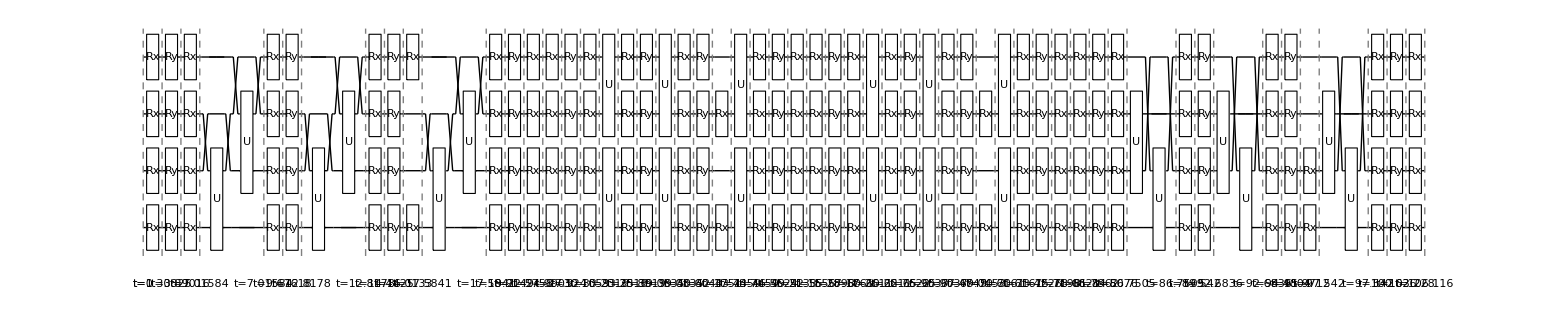

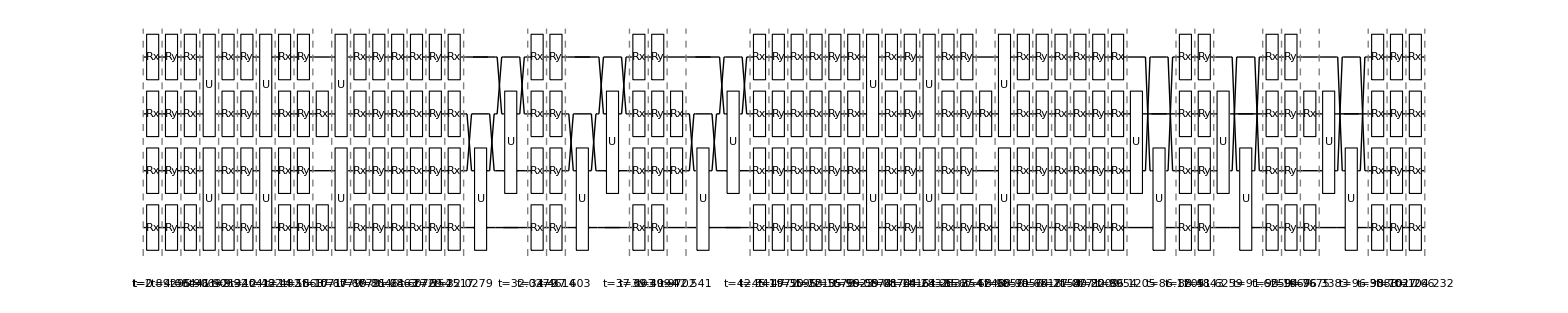

{Layer,4,0,16}

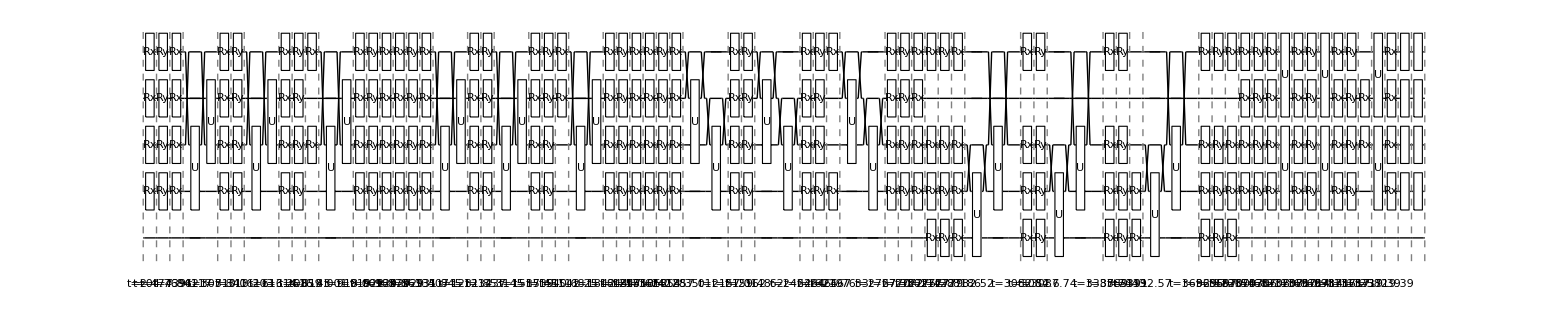

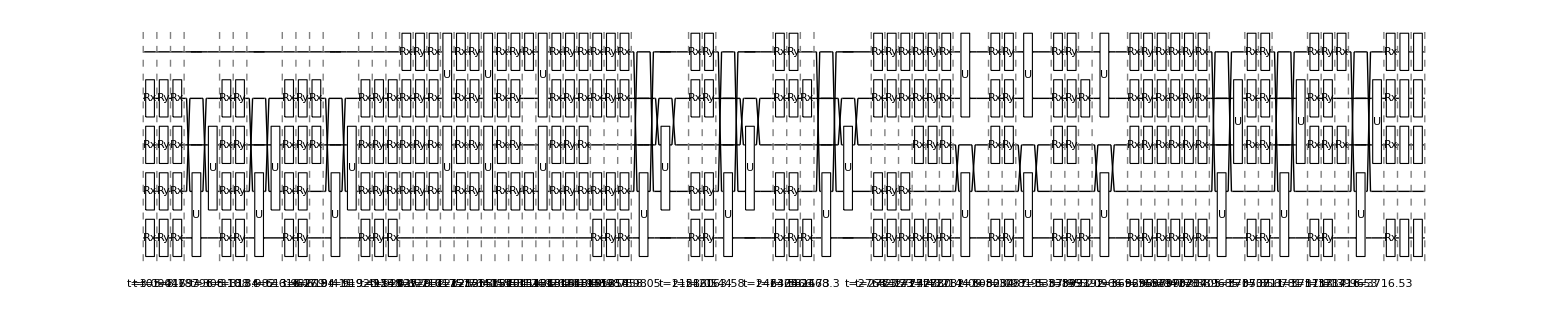

{Layer,5,32,32}

{{{4,0.814469,0.163797},{4,0.870583,0.171471},{4,0.0645521,0.00194998}},{{5,0.760167,0.025754},{5,0.819865,0.0225943},{5,0.0728342,0.00293053}}}

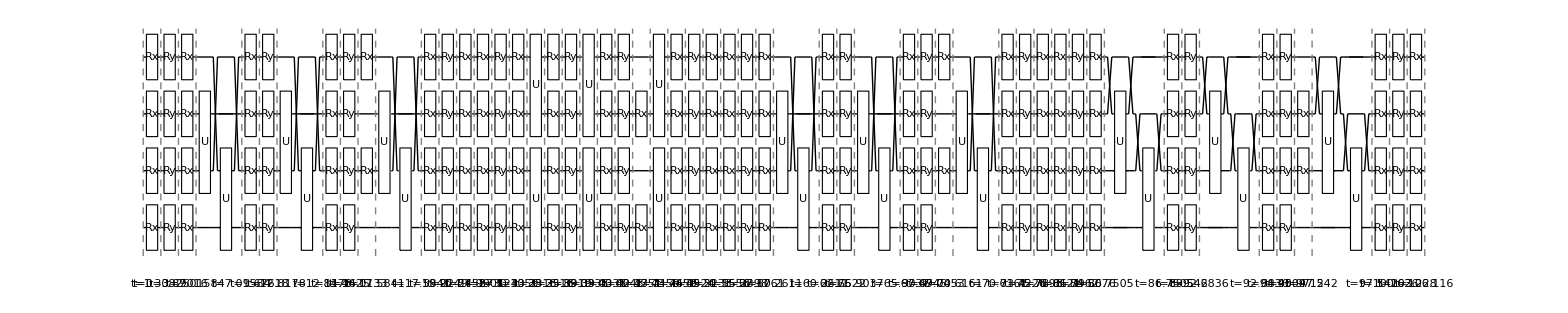

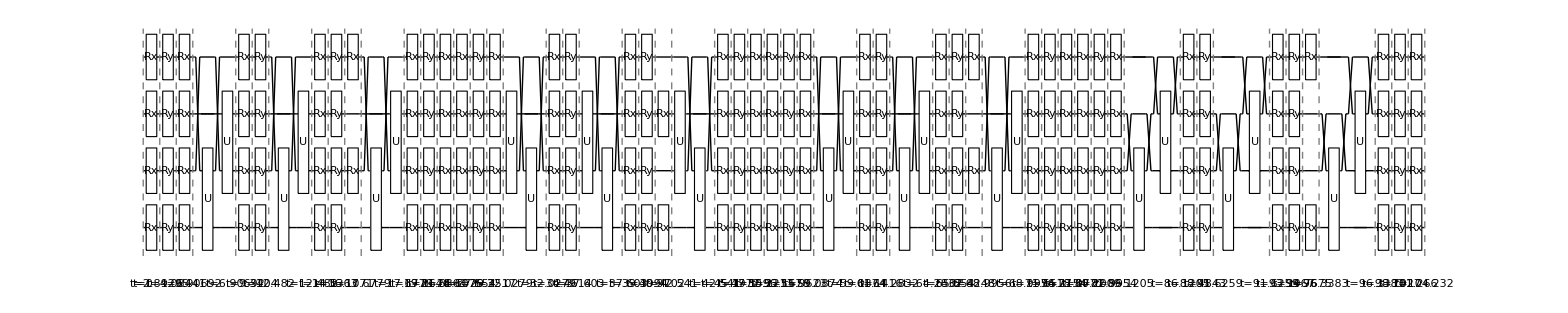

{Layer,4,16,16}

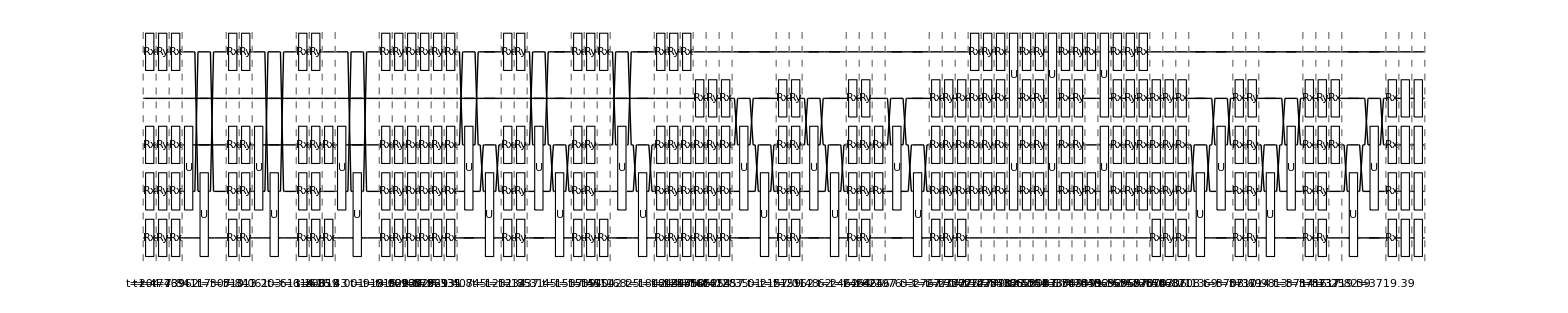

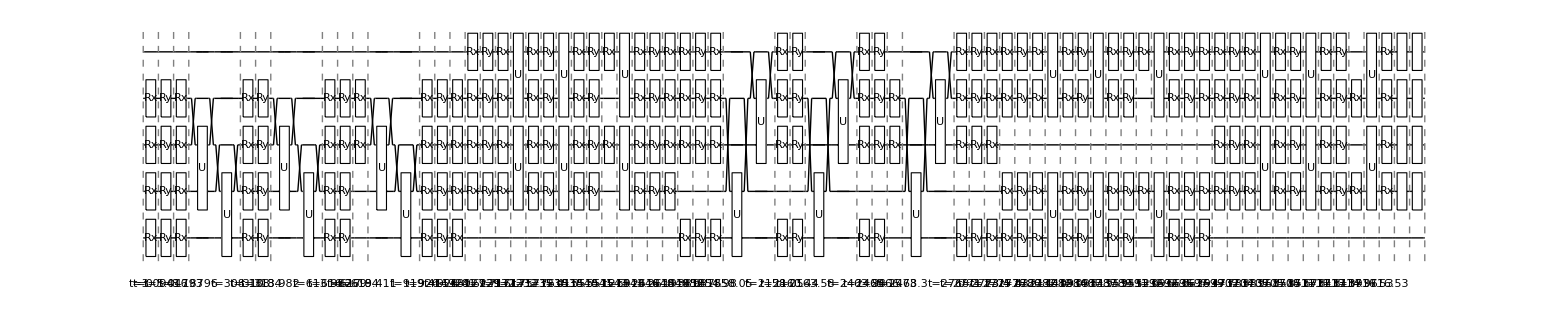

{Layer,5,32,32}

{{{4,0.805263,0.0629829},{4,0.845807,0.0641924},{4,0.0479559,0.00110484}},{{5,0.733081,0.0179803},{5,0.77557,0.0195731},{5,0.0547827,0.000335585}}}

```mathematica
(*Generating and applying the circuits to a register and getting the probability of a heavy output*)
QVProcedure[DataSet_,NQ_, MaxNQ_,NReps_,Reg_,ConnectivityRule_]:=Table[
Circ1=QVCirc[DataSet[[NQ*Quotient[NQ,2]*Rep+1;;NQ*Quotient[NQ,2]*(Rep+1)]],NQ,ConnectivityRule];
(*Print[Circ1];*)
Initialisation=InitCirc[Reg,MaxNQ];
InitCircuit=Flatten[Join[Initialisation,Circ1]];
CircNoisy=ExtractCircuit[InsertCircuitNoise[InitCircuit,RydDev,ReplaceAliases->True]];
CircModel=ExtractCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]];
Print[DrawCircuit[GetCircuitSchedule[Circ1,RydDev,ReplaceAliases->True]]];
SetQuregMatrix[Reg,RandomMixState[MaxNQ]];
ApplyCircuit[Reg,CircNoisy];
PoutcomesNoisy=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
(*Print[PoutcomesNoisy];*)
InitZeroState[Reg];
(*Print[DrawCircuit[CircModel]];*)
ApplyCircuit[Reg,CircModel];
PoutcomesModel=CalcProbOfAllOutcomes[Reg,Range[0,NQ-1]];
PNoLoss=Total[PoutcomesNoisy];
PoutcomesNoisyRen=PoutcomesNoisy/PNoLoss;
(*Print[NQ, " Model Outcomes Probabilities ",PoutcomesModel," Noisy Outcome Probabilities ",PoutcomesNoisy];*)
HeavyOutputs=CheckHeavyOutputProb[PoutcomesNoisy,PoutcomesModel];
HeavyOutputsRen=CheckHeavyOutputProb[PoutcomesNoisyRen,PoutcomesModel];
{Total[HeavyOutputs],Total[HeavyOutputsRen],1-PNoLoss},{Rep,0,NReps-1,1}]


(*Put everything together and get a value for Quantum Volume*)
QVCalc[DataSet_,MaxNQ_,NReps_,ConnectivityRule_]:=Table[ρ=CreateDensityQureg[MaxNQ];
HOP=QVProcedure[DSSplice=DataSet[[(Total[Table[a*Quotient[a,2],{a,0,NQ-1}]]*NReps)+1 ;;Total[Table[a*Quotient[a,2],{a,0,NQ}]*NReps]]],NQ,MaxNQ,NReps,ρ,ConnectivityRule];
DestroyAllQuregs[];
MHOP=Mean[HOP[[All,1]]];
MHOPRen=Mean[HOP[[All,2]]];
MPLoss=Mean[HOP[[All,3]]];
σPLoss=StandardDeviation[HOP[[All,3]]]/Sqrt[NReps-1];
σ=StandardDeviation[HOP[[All,1]]]/Sqrt[NReps-1];
σRen=StandardDeviation[HOP[[All,2]]]/Sqrt[NReps-1];
If[ Re[(MHOP-2σ)]>2/3,VQ=2^NQ,VQ=0];
If[ Re[(MHOPRen-2σRen)]>2/3,VQRen=2^NQ,VQRen=0];
Print[{"Layer",NQ,VQ,VQRen}];
{{NQ,MHOP,2σ},{NQ,MHOPRen,2σRen},{NQ,MPLoss,σPLoss}}
,{NQ,4,5,1}];

(*ARPA2AQV=QVCalc[data,9,200,"ARPA2A"]
ARPSWAPQV=QVCalc[data,9,200,"ARPSWAP"]*)
(*PIA2AQV=QVCalc[data,9,200,"PIA2A"]
PISWAPQV=QVCalc[data,9,200,"PISWAP"]*)

ARPParMoveQV=QVCalc[data,9,2,"ARPParMove"]
PIParMoveQV=QVCalc[data,9,2,"PIParMove"]
DestroyAllQuregs[];
```

```mathematica
(*Old data storage*)
```

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,512}

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,512}

{{2,0.786021,0.0139088},{3,0.847087,0.0123368},{4,0.831373,0.00726228},{5,0.850482,0.00577239},{6,0.839353,0.00380182},{7,0.841118,0.00336454},{8,0.828258,0.00189946},{9,0.825211,0.0014891}}

```mathematica
ARPMoveQV
```

{{2,0.797108,0.0128986},{3,0.851692,0.0124526},{4,0.837986,0.00759597},{5,0.855545,0.00517676},{6,0.843309,0.00339957},{7,0.846971,0.00304184},{8,0.832896,0.00208175},{9,0.831794,0.00152376}}

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,128}

{Layer,8,256}

{Layer,9,512}

{Layer,2,4}

{Layer,3,8}

{Layer,4,16}

{Layer,5,32}

{Layer,6,64}

{Layer,7,0}

{Layer,8,0}

{Layer,9,0}

```mathematica
MeanRenormPIMove=Table[Mean[RenormFactorPIMove[[i]]],{i,1,Length[RenormFactorPIA2A]}]
MeanRenormARPSWAP=Table[Mean[RenormFactorARPSWAP[[i]]],{i,1,Length[RenormFactorARPSWAP]}]
```

{0.0665524,0.0692619,0.0825512,0.0876574,0.108157,0.115759,0.143205,0.152819,Mean[{}]}

```mathematica
?QuEST`Gates
```

Missing[UnknownSymbol,QuEST`Gates]

```mathematica
CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{Subscript[CZH, 0,1]},RydDev,ReplaceAliases->True]]]
```

CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{CZH_(0,1)},RydDev,ReplaceAliases→True]]]

```mathematica
ARPA2AQVUnNorm={{2,0.7405816455278738,0.012891402234974744},{3,0.7763156324179025,0.010735056357840861},{4,0.7496847408842636,0.006620655826557423},{5,0.7626388038383476,0.0051446438862961},{6,0.7277371459047844,0.002728320896540523},{7,0.7198160946731358,0.002559978776835931},{8,0.6735455321130638,0.0014137201886522943},{9,0.6608622975551284,0.0011299567629418342}}
```

{{2,0.740582,0.0128914},{3,0.776316,0.0107351},{4,0.749685,0.00662066},{5,0.762639,0.00514464},{6,0.727737,0.00272832},{7,0.719816,0.00255998},{8,0.673546,0.00141372},{9,0.660862,0.00112996}}

```mathematica
ARPSWAPQVUnNorm={{2,0.734151602191516,0.012203688063819421},{3,0.7796258146926748,0.0114042182741467},{4,0.7584907533431214,0.0066033072782086056},{5,0.7467017004789538,0.005105813066262238},{6,0.6881346044369444,0.003464302233772094},{7,0.6614145781024228,0.0028625009400299085},{8,0.5888492972994888,0.0024423096373259057},{9,0.5588482658031424,0.002553979984975081}}
ARPMoveQVUnNorm={{2,0.7316097045776994,0.012453361680376711},{3,0.7912486808307285,0.011152390054086006},{4,0.7565998978239634,0.006552142857848809},{5,0.7587936023582366,0.004799933512465381},{6,0.7248659575145965,0.0031892410072394428},{7,0.7153719352535137,0.0024610562966784896},{8,0.665925680366202,0.0015435275606227416},{9,0.6507702335994054,0.0011162694769176094}}
```

{{2,0.734152,0.0122037},{3,0.779626,0.0114042},{4,0.758491,0.00660331},{5,0.746702,0.00510581},{6,0.688135,0.0034643},{7,0.661415,0.0028625},{8,0.588849,0.00244231},{9,0.558848,0.00255398}}

{{2,0.73161,0.0124534},{3,0.791249,0.0111524},{4,0.7566,0.00655214},{5,0.758794,0.00479993},{6,0.724866,0.00318924},{7,0.715372,0.00246106},{8,0.665926,0.00154353},{9,0.65077,0.00111627}}

```mathematica
PIA2AQVUnNorm={{2,0.7401509835586911,0.011720393627843191},{3,0.7861195373963302,0.010947768305616145},{4,0.7735466762741807,0.006139049269876257},{5,0.7755597101341623,0.004957302000898714},{6,0.7540040405551361,0.0032992294402544075},{7,0.7517134081713516,0.0025793579054604354},{8,0.7184799655663686,0.0017272340009129104},{9,0.7097760794016982,0.001339681908122264}}
```

{{2,0.740151,0.0117204},{3,0.78612,0.0109478},{4,0.773547,0.00613905},{5,0.77556,0.0049573},{6,0.754004,0.00329923},{7,0.751713,0.00257936},{8,0.71848,0.00172723},{9,0.709776,0.00133968}}

```mathematica
PISWAPQVUnNorm={{2,0.7435531945073748,0.011901007879567028},{3,0.7940027426701181,0.010321949703200325},{4,0.7659901802837689,0.007085147237230059},{5,0.7647139244545597,0.005664124187713016},{6,0.7273886156772132,0.003525305196753448},{7,0.712418857446769,0.0028805781172344053},{8,0.6550670104692926,0.002483069085888343},{9,0.6322294208564452,0.0023273933185776912}}
```

{{2,0.743553,0.011901},{3,0.794003,0.0103219},{4,0.76599,0.00708515},{5,0.764714,0.00566412},{6,0.727389,0.00352531},{7,0.712419,0.00288058},{8,0.655067,0.00248307},{9,0.632229,0.00232739}}

```mathematica
PIMoveQVUnNorm={{2,0.7359837396494435,0.012665090894074575},{3,0.7904297004887582,0.010958052382184134},{4,0.7677433251358556,0.0064855437900339435},{5,0.7800894334429009,0.005242273136270247},{6,0.7509344297889435,0.00316174524209156},{7,0.743504677658759,0.002576245716119806},{8,0.7094708481092695,0.001627629659813381},{9,0.699616183100201,0.0012965356275318977}}
```

{{2,0.735984,0.0126651},{3,0.79043,0.0109581},{4,0.767743,0.00648554},{5,0.780089,0.00524227},{6,0.750934,0.00316175},{7,0.743505,0.00257625},{8,0.709471,0.00162763},{9,0.699616,0.00129654}}

```mathematica
MeanRenormPIA2A={0.0665402220585088,0.06936915034994637,0.08246500313651679,0.08761588246300792,0.10826942876131372,0.11587803153320925,0.14314265212040853,0.15274980616844716}
```

{0.0665402,0.0693692,0.082465,0.0876159,0.108269,0.115878,0.143143,0.15275}

```mathematica
MeanRenormPISWAP={0.06651223359498336,0.06933340641705779,0.08250450816446736,0.09732735475716929,0.1327290665614612,0.15529831976987418,0.20326674227961392,0.2262761074503026}
```

{0.0665122,0.0693334,0.0825045,0.0973274,0.132729,0.155298,0.203267,0.226276}

```mathematica
MeanRenormPIMove={0.06655241346304827, 0.06926191675755718,0.08255116333487107,0.0876574148000778,0.10815734991256716,0.11575895425630245,0.14320458424230437,0.15281919753058623}
```

{0.0665524,0.0692619,0.0825512,0.0876574,0.108157,0.115759,0.143205,0.152819}

```mathematica
MeanRenormARPA2A={0.07074940104421311,0.0755396303625562,0.09888697829524155,0.10773031675463329,0.14362599160166237,0.15670331182186956,0.202718259758029,0.21866533363205387}
MeanRenormARPSWAP={0.07072197687583025,0.07560784800815645,0.09885574096018666,0.125646199165414,0.1835367688844255,0.220735713103119,0.29815794264489387,0.3334822180218006}
MeanRenormARPMove={0.0707452085914006,0.07567024425526565,0.09854171621276976,0.10788256103612998,0.14333651197132707,0.1562577981098641,0.20274888369740773,0.21864817610273504}
```

{0.0707494,0.0755396,0.098887,0.10773,0.143626,0.156703,0.202718,0.218665}

{0.070722,0.0756078,0.0988557,0.125646,0.183537,0.220736,0.298158,0.333482}

{0.0707452,0.0756702,0.0985417,0.107883,0.143337,0.156258,0.202749,0.218648}

```mathematica
ARPA2AQVRenorm={{2,0.79079121496538±0.013524801785153353},{3,0.8489587791370138±0.011987730709441608},{4,0.8384361547827764±0.0070229755998004635},{5,0.8566745449343114±0.005393198979184408},{6,0.8500726204105155±0.003827795673738825},{7,0.8542196981782405±0.002813378105357417},{8,0.8441067931395366±0.001997463066941062},{9,0.8454409614573727±0.0013928806307027552}}
ARPSWAPQVRenorm={{2,0.7922549774371156±0.0141165918715427},{3,0.8472778724587833±0.01245063626803773},{4,0.8311756513202974±0.007313345567025717},{5,0.8596835903542691±0.005757862880054895},{6,0.8460001982372652±0.0043378621102428665},{7,0.8499306186085411±0.0038228215163547802},{8,0.8374276975058441±0.003750293688273244},{9,0.8354296432289274±0.0034930655432672216}}
ARPMoveQVRenorm={{2,0.797107593010428±0.012898644132759601},{3,0.851691990239746±0.012452588177536217},{4,0.8379864267360843±0.0075959651136756805},{5,0.855544552071303±0.005176758865118236},{6,0.8433089449367895±0.0033995744773940182},{7,0.8469706618475393±0.003041835600156929},{8,0.8328961760327086±0.00208175486602617},{9,0.8317938000779861±0.001523759850160512}}
```

{{2,0.790791±0.0135248},{3,0.848959±0.0119877},{4,0.838436±0.00702298},{5,0.856675±0.0053932},{6,0.850073±0.0038278},{7,0.85422±0.00281338},{8,0.844107±0.00199746},{9,0.845441±0.00139288}}

{{2,0.792255±0.0141166},{3,0.847278±0.0124506},{4,0.831176±0.00731335},{5,0.859684±0.00575786},{6,0.846±0.00433786},{7,0.849931±0.00382282},{8,0.837428±0.00375029},{9,0.83543±0.00349307}}

{{2,0.797108±0.0128986},{3,0.851692±0.0124526},{4,0.837986±0.00759597},{5,0.855545±0.00517676},{6,0.843309±0.00339957},{7,0.846971±0.00304184},{8,0.832896±0.00208175},{9,0.831794±0.00152376}}

```mathematica
PIA2AQVRenorm={{2,0.7895406850254238±0.013737026566374662},{3,0.8495997028586166±0.012012553913266884},{4,0.8348508349866097±0.0070277610166078665},{5,0.8555165135009669±0.005663812268499948},{6,0.8445639541713855±0.00408156530877206},{7,0.8511686618078806±0.0029856417429019286},{8,0.8379757405830542±0.002150526821011032},{9,0.8378251734924934±0.001512796740746905}}

PISWAPQVRenorm={{2,0.7902552437379439±0.01384407174922472},{3,0.8486659579417659±0.012215787267853688},{4,0.8382793607760826±0.006704505388549647},{5,0.846127939207912±0.005854623275864581},{6,0.8464296908209206±0.004054319642496805},{7,0.8390873816070714±0.0037142443321610094},{8,0.8260365898542622±0.003011805797972457},{9,0.8166398081285762±0.003156891926526585}}
PIMoveQVRenorm={{2,0.7860211890945226±0.013908767589961903},{3,0.8470873110638029±0.012336846799916618},{4,0.8313732663443375±0.007262278323814587},{5,0.85048199725319±0.0057723893095098285},{6,0.8393529806487345±0.00380181720776509},{7,0.8411178138896994±0.0033645361481727297},{8,0.8282576131424173±0.0018994634645571667},{9,0.8252110631170132±0.0014891011166331073}}
```

{{2,0.789541±0.013737},{3,0.8496±0.0120126},{4,0.834851±0.00702776},{5,0.855517±0.00566381},{6,0.844564±0.00408157},{7,0.851169±0.00298564},{8,0.837976±0.00215053},{9,0.837825±0.0015128}}

{{2,0.790255±0.0138441},{3,0.848666±0.0122158},{4,0.838279±0.00670451},{5,0.846128±0.00585462},{6,0.84643±0.00405432},{7,0.839087±0.00371424},{8,0.826037±0.00301181},{9,0.81664±0.00315689}}

{{2,0.786021±0.0139088},{3,0.847087±0.0123368},{4,0.831373±0.00726228},{5,0.850482±0.00577239},{6,0.839353±0.00380182},{7,0.841118±0.00336454},{8,0.828258±0.00189946},{9,0.825211±0.0014891}}

```mathematica
RenormFactorARPSWAP
```

{{},{},{},{},{},{},{},{}}

```mathematica
CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{Subscript[CZARP, 0,1]},RydDev,ReplaceAliases->True]]]
```

```mathematica
CalcCircuitMatrix[ExtractCircuit[InsertCircuitNoise[{Subscript[CZARP, 0,1]},RydDev,ReplaceAliases->True]]]
```

```mathematica
IdealHOP=Table[{i,(1+Log[2])/2},{i,2,9}];
Thresh=Table[{i,2/3},{i,2,9}];
```

```mathematica
ListLinePlot[{ARPA2AQVRenorm,ARPSWAPQVRenorm,ARPMoveQVRenorm,Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"ARP A2A","ARP SWAP","ARP Move","2/3 Threshold","Ideal HOP"}]
ListLinePlot[{PIA2AQVRenorm,PISWAPQVRenorm,PIMoveQVRenorm,Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Parallel Implementation A2A","Parallel Implementation SWAP","Parallel Implementation Move","2/3 Threshold","Ideal HOP"}]
```

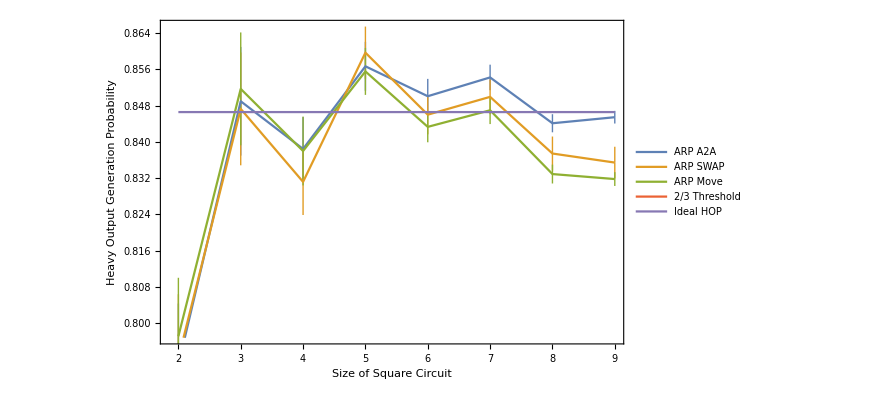

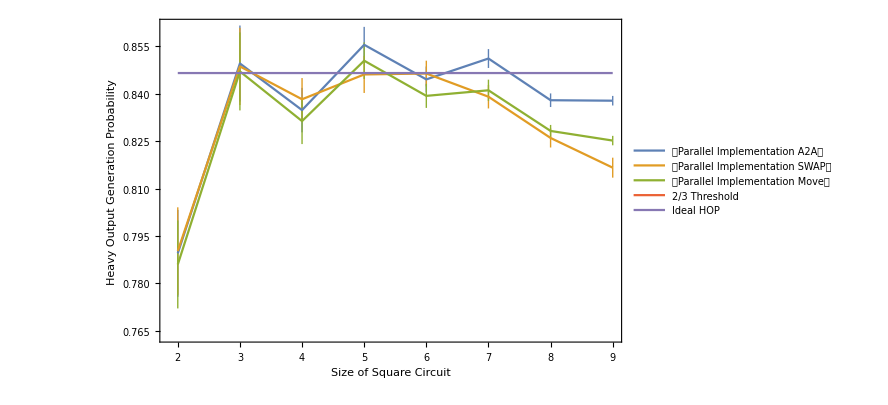

```mathematica
ErrorBar[DataSet_]:=Table[{DataSet[[i,1]],DataSet[[i,2]]±DataSet[[i,3]]},{i,1,Length[DataSet]}]
ListLinePlot[{ErrorBar[ARPA2AQVUnNorm],ErrorBar[ARPSWAPQVUnNorm],ErrorBar[ARPMoveQVUnNorm],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"ARP A2A","ARP SWAP","ARP Move","2/3 Threshold","Ideal HOP"}]
ListLinePlot[{ErrorBar[PIA2AQVUnNorm],ErrorBar[PISWAPQVUnNorm],ErrorBar[PIMoveQVUnNorm],Thresh,IdealHOP},AxesLabel->{HoldForm[Layer Depth],HoldForm[Heavy Output Generation Probability]},Frame->True,FrameLabel->{"Size of Square Circuit","Heavy Output Generation Probability"},PlotLegends->{"Parallel Implementation A2A","Parallel Implementation SWAP","Parallel Implementation Move","2/3 Threshold","Ideal HOP"}]
```

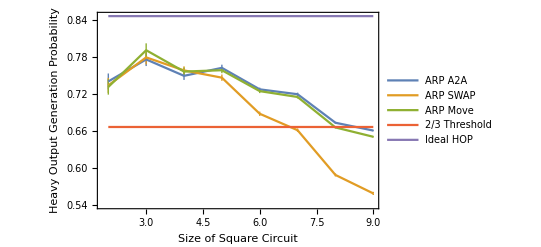

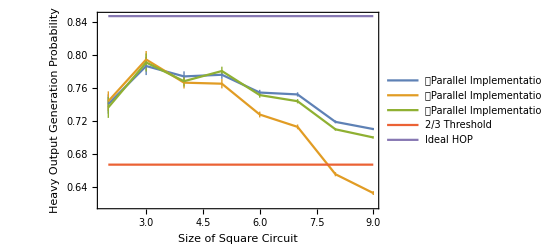

```mathematica
PlusMinus[1]
```

±1

```mathematica
RandomSample[{{0,1},{2,3},{4,5},{6,7},{8}}]
```

{{0,1},{2,3},{8},{4,5},{6,7}}

```mathematica
ReverseSortBy[Map[Sort,Partition[RandomSample[Range[0,9-1],9],UpTo[2]]],Length]
```

{{5,8},{4,6},{1,2},{0,7},{3}}

```mathematica
NRandQubitPairs[NQ_]:=ReverseSortBy[Map[Sort,Partition[RandomSample[Range[0,9-1],9],UpTo[2]]],Length]
```

```mathematica
NRandQubitPairsOrdered[NQ_]:=Table[A=NRandQubitPairs[9];Join[Sort[A[[1;;4]]],{A[[5]]}],{i,1,1}][[1]]
```

```mathematica
NRandQubitPairsOrdered[9]
```

{{0,7},{1,5},{3,6},{4,8},{2}}

```mathematica
Partition[{2,4,8,1,7,0,3,5,6},2]
```

{{2,4},{8,1},{7,0},{3,5}}

```mathematica
?Module
```

```mathematica
?Replace
```

```mathematica
If[1==1,Print[True],Print[False]]
```

True